Using the bathtub model and cellular automata (CA) approach, the project models the changing water levels of a region, and highlights which areas will become flooded.

## Introduction

Flooding in urban areas may cause severe damage to infrastructure and uproot communities. Cities by the ocean also regularly face coastal flooding. Accurate modeling of water flow is crucial for various applications, such as urban planning, flood prediction, and water resource management. With increased flood rates around the world, We model water runoff using two different approaches: a bathtub inundation model and a cellular automata model.  
We want to visualize regions that will get the most water during heavy rainfall. The model assumes uniform rainfall, and hydrological losses are not considered. By incorporating the bathtub model into our framework, we ensure that water is distributed uniformly over the simulated area, facilitating an initial estimation of water accumulation and infiltration. Using a weighted cellular automata model enables a more realistic representation of water flow dynamics, accounting for the physical limitations on water velocity through the use Manning’s formula and the critical flow equation.

#### Locations

We ran the model over the following locations:

Atlantic City, NJ

Delaware River(PA & NJ)

Princeton, NJ

## Elevation Bathtub Model

To start, I used the simple bathtub inundation model to display the purpose of the project, which is to show where water will food when the water level is raised. The model assumes that the areas will be inundated if their elevation is below the projected water level.

#### Atlantic City

Atlantic City is a coastal resort city in New Jersey, know for its many casinos, wide beaches, and Boardwalk. It is frequently flooded by the Atlantic Ocean, especially with the ocean rising at faster rates in the future.

We access Wolfram' s GeoElevationData for Atlantic City, that is stored in a 2 D Quantity Array :

```mathematica
data=GeoElevationData[,GeoRange->Quantity[5, "Kilometers"],GeoProjection->Automatic];
```

Here, we created a visualization that allows you to manipulate the sea level to observe which regions will be flooded. We used the Manipulate, ListPlot3D to plot the GeoElevationData, and used ColorFunction to set regions below sea level to blue.

```mathematica
Manipulate[ListPlot3D[Reverse[data],MeshFunctions->{#&},Mesh->30,ImageSize->Medium,ColorFunction->Function[{x,y,z},If[z<=sealevel,ColorData["DeepSeaColors"][0.1z+2],RGBColor["#a38672"]]],ColorFunctionScaling->False],{sealevel,0,10},SaveDefinitions->True]
```

We can also visualize this in 2D, using a ReliefPlot.

```mathematica
Manipulate[ReliefPlot[data, ColorFunction->Function[{x},If[x<=sealevel,ColorData["DeepSeaColors"][0.1x+2],ColorData["SandyTerrain"][0.1x]]],ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Elevation"],{After,Top}]],{sealevel,0,10},SaveDefinitions->True]
```

#### Delaware River

We will also apply the bathtub model to the Delaware River in the East Coast of the US.

We generate a list of coordinates based on the part of the Delaware River we want to focus. We will focus on the Pennsylvania-New Jersey section, stretching from New Hope, PA, to Hopewell, NJ:

```mathematica
DEcoords=Table[{x,y},{x,40.188083,40.353025,.001},{y,-74.959693,-74.730801}];
```

Then, We get the GeoPosition at the coordinates so We can use GeoElevationData on our coordinates.

```mathematica
DEdata= GeoElevationData[GeoPosition/@Flatten[DEcoords,1]];
```

We’ll visualize this again in 3D and 2D.

```mathematica
Manipulate[ListPlot3D[Reverse[DEdata],MeshFunctions->{#&},Mesh->30,ImageSize->Medium,ColorFunction->Function[{x,y,z},If[z<=sealevel,ColorData["DeepSeaColors"][0.01z],ColorData["SandyTerrain"][0.001z+0.6]]],ColorFunctionScaling->False,PlotLegends->Automatic],{sealevel,50,600,10},SaveDefinitions->True]
```

```mathematica
Manipulate[ReliefPlot[DEdata,ColorFunction->Function[{x},If[x<=sealevel,ColorData["DeepSeaColors"][0.01x],ColorData["SandyTerrain"][0.001x+0.6]]],ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Elevation"],{After,Top}]],{sealevel,50,600,10},SaveDefinitions->True]
```

Since water flow has many other factors than just elevation, it wouldn’t just go where the lowest elevation is. While the bathtub model captures the the general idea of where water will travel, our cellular automata model will consider more factors of how water flows and more accurately predict water spread and flooding.

## Cellular Automata Approach

We used a Cellular Automata(CA) approach to simulate flooding across a region due to heavy rainfall (pluvial flooding) in 2D. Cellular automata are discrete models that simulate the behavior of individual cells based on predefined rules. The model divides the area of land into a discrete space of square grid cells. We will take the Von Neumann neighborhood for each cell, meaning a central cell has 4 neighbor cells adjacent to it. Water flows from the central cell to neighboring cells depending on the water flow rules that the model will set.

Data

Elevation - given by GeoElevationData --> constant

Water Depth - we add a certain amount --> changing

Water Level = Elevation + Water Depth --> what we compare

-Graphics-

Each point in this graph represents one cell of water, whose volume will depend on the size of our dataset.

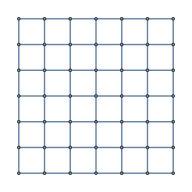

```mathematica
graph=GridGraph[{7,7}]
```

The neighbors function returns the list of vertices that neighbors the center cell parameter:

```mathematica
neighbors[center_]:=Drop[VertexList[NeighborhoodGraph[graph,center]],1]
```

For example, consider vertex 9.  NeighborhoodGraph will show the 4 neighbors of vertex 9. Here, vertex 9 is colored red.

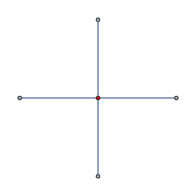

```mathematica
NeighborhoodGraph[GridGraph[{7,7},VertexStyle->{9->Red}],9]
```

## Simple Cellular Automata Model

#### Rule

The guiding transition rule of this model is for a central cell to give its neighboring cells 1 unit of water depth if it has a higher water level than its neighbor. Then, We apply this rule to every cell in the grid, iterating until the water depths are relatively constant.

Note that center cells will only give away water, and neighbor cells will only receive water.

So, upstream cells (higher water level than center) aren’t changed, and downstream cells will get water.

#### Data

For this model, we will be using a much smaller dataset of Atlantic City, a 7 by 7 2D array.

```mathematica
smelevdata=GeoElevationData[,GeoRange->Quantity[100,"Meters"],GeoProjection->Automatic];
smelevdata=Flatten[QuantityMagnitude[Normal@smelevdata]];
```

We will have two versions of this model: one that updates each cell one by one, which is not as accurate since water doesn’t flow from one cell, rather all at once since it is coming from above, and one that updates the cells simultaneously. The first model helps us visualize what is actually going on at every step.

#### Step By Step Model

Helper Functions

We define two helper functions for the rule: add, which adds one to the value at waterdepths, and subtract, which subtracts one.

```mathematica
add1[i_]:=ReplacePart[waterdepths,i->waterdepths[[i]]+1];
subtract1[i_]:=ReplacePart[waterdepths,i->waterdepths[[i]]-1];
```

Rule Function
Here is the rule for the first simple model we will make.

The rule goes through each neighbor cell of the center cell, which is passed as a parameter. Each neighbor cell is updated based on a water level comparison to the center cell. Note the center cell will not give water if it is less than 1, otherwise its water depth will be negative, which is not possible.

```mathematica
smrule1[center_]:=Table[
If[
smelevdata[[center]]+waterdepths[[center]]>smelevdata[[x]]+waterdepths[[x]],If[waterdepths[[center]]>=1,
waterdepths=add1[x];waterdepths=subtract1[center];]
],
{x,neighbors[center]}
]
```

Visualization
We will plot the new waterdepths and elevation using BarChart3D. We stack the waterdepth over the elevation, to see what water will look like on the land we took. ** needs editing

waterdepths is set to 5 at cell, representative of the amount of uniform rainfall.

Before running the model, we reset the values of waterdepths.

```mathematica
waterdepths=Table[5,49];
```

```mathematica
style={ChartLayout->"Grid",Method->{"Canvas"->False},BarSpacing->{.1,.1}};
```

To do this, we use ListAnimate and iterate through every step . One iteration is when every cell becomes the center cell once; it goes from 1 to 49, updating the waterdepths values each time . This allows us to see what it going on at each step .

```mathematica
ListAnimate[First/@Table[{Show[BarChart3D[Partition[smelevdata,7],style,ColorFunction->"SiennaTones",ChartElementFunction->Function[{xyz,z},{Cuboid@@Transpose@xyz}]],BarChart3D[Partition[waterdepths+smelevdata,7],style,ColorFunction->"DeepSeaColors",ChartElementFunction->Function[{xyz,z},{Opacity[.5],Cuboid@@Transpose@(0.0015223+0.999123 xyz)}]],ImageSize->Large],smrule1[#]&/@Range[49];},{x,1,10}],SaveDefinitions->True]
```

As you can see, the water appears to build up towards a corner. This is because as we are updating cells one by one from cell 1-49, so the water moves across the grid. As we iterate more times, the water levels eventually become constant.

#### Simultaneously Updated Model

In this model, we use the same rules, except the waterdepths values are not being updated until the end of the iteration. This ensures that water is flowing uniformly from everything in the grid, like rainfall, and not moving across a grid, as if water is beginning one place and moving to the opposite corner.

To do this, we create a copy of waterdepths called tempwaterdepths, which will store the changes of one iteration. However, the comparisons will continue to use waterdepths values. At the end of the iteration, we simultaneously update waterdepths to tempwaterdepths.

Helper Functions

The helper functions stay the same, except it modifies the tempwaterdepth, which stores temporary alterations of an iteration.

```mathematica
tempwaterdepth=waterdepths;
```

```mathematica
add[i_]:=ReplacePart[tempwaterdepth,i->tempwaterdepth[[i]]+1];
subtract[i_]:=ReplacePart[tempwaterdepth,i->tempwaterdepth[[i]]-1];
```

Rule

The rule is similar, except we are storing changes in tempwaterdepth. Note that we use waterdepths to compare water levels, but use tempwaterdepth to check if it is greater than 1 to ensure we aren’t subtracting too much.

```mathematica
smrule2[center_]:=Table[
If[
smelevdata[[center]]+waterdepths[[center]]>smelevdata[[x]]+waterdepths[[x]],If[tempwaterdepth[[center]]>=1,
tempwaterdepth=add[x];tempwaterdepth=subtract[center];]
],
{x,neighbors[center]}
]
```

A function to update waterdepths after a full iteration:

```mathematica
update[]:=Table[
smrule2[x];waterdepths=tempwaterdepth,{x,49}]
```

Visualization

```mathematica
waterdepths=Table[5,49];
tempwaterdepth=waterdepths;
```

```mathematica
ListAnimate[First/@Table[{Show[BarChart3D[Partition[smelevdata,7],style,ColorFunction->"SiennaTones",ChartElementFunction->Function[{xyz,z},{Cuboid@@Transpose@xyz}]],BarChart3D[Partition[waterdepths+smelevdata,7],style,ColorFunction->"DeepSeaColors",ChartElementFunction->Function[{xyz,z},{Opacity[.5],Cuboid@@Transpose@(0.0015223+0.999123 xyz)}]],ImageSize->Large],Table[update[],x];},{x,1,5}],SaveDefinitions->True]
```

## Weighted Cellular Automata Model

Now, we will use a more complex cellular automata model to display the water flow. This model, called WCA2D, Weighted Cellular Automata 2D, uses a weight computing system and physical limitations to model water flow without too complex mathematical equations and fluid dynamics concepts (Guidolin et al., 2016).

In the model, the ratios of water are transferred from the central cell to the downstream neighbor cells using a weight-based system.

The water transferred will be limited by Manning’s formula and the critical flow equation, to produce a more accurate prediction of resulting water levels.

#### Collecting Data

```mathematica
elevationdata=GeoElevationData[,GeoRange->Quantity[100,"Meters"],GeoProjection->Automatic];
elevationdata=Flatten[QuantityMagnitude[Normal@elevationdata]];
elevationdata=elevationdata-Min[elevationdata];
```

Each coordinate point, with a corresponding elevation, constitutes a cell:

```mathematica
graph = GridGraph[{7,7}];
```

The area of a cell is defined by the area of region/number of cells:

```mathematica
area=100/Length[elevationdata];
```

```mathematica
edgelength=Sqrt[area];
```

A small tolerance to set to help reduce oscillation. Downstream cells whose water levels are within tolerance of the center cell will be ignored, and won’t receive water.

Define tolerance:

```mathematica
tolerance=0.1;
```

Sets initial waterdepth to 5 at every cell(e.g. 5 in of rainfall)

```mathematica
waterdepth=Table[5,49];
```

Note that in our model, 5 represents 5ft. Although not realistic, it proves easier to visualize.

#### Algorithm

To distribute the volume being transferred from the central cell to the neighborhood,  we use a weighting system. 
1) Identify downstream cells
2) Compute weights based on available storage volume
3) Compute total volume leaving central cell
4) For each downstream cell, calculate the new intercellular-volume

We use the following helper functions to accomplish this:

#### Identifying Downstream Cells

Finds the difference in water level(elevation+waterdepth) between center and ith neighbor:

```mathematica
waterleveldiff[center_,i_] := (elevationdata[[center]] + waterdepth[[center]]) - (elevationdata[[i]] + waterdepth[[i]])
```

Available storage volume is the possible volume a neighbor cell can store from the center cell. Note that this value will be 0 for upstream cells since neighbor cells never give water. It is the water level difference, which is in m, multiplied by area (m^2).

Note that if there are no eligible cells to receive water(either upstream or doesn’t satisfy tolerance), this value is set to 0.

Finds available storage volume of the ith neighbor cell of center:

```mathematica
availstoragevol[center_,i_]:=Max[waterleveldiff[center,i],0]*area
```

Determines whether a center cells has downstream cells:

```mathematica
upstream[center_]:=If[Select[neighbors[center],waterleveldiff[center,#]>tolerance&]=={},True,False]
```

### Weight Computing

#### Helper Functions

Finds the minimum available storage volume between all the neighbor cells of a center cell:

```mathematica
minstoragevol[center_]:=area*With[{list=Select[waterleveldiff[center,#]
	&/@neighbors[center],#>tolerance&]},
	If[list=={},0,Min[list]]]
```

Finds the maximum available storage volume(used later but not in weights):

```mathematica
maxstoragevol[center_]:=area*With[{list=Select[waterleveldiff[center,#]
	&/@neighbors[center],#>tolerance&]},
	If[list=={},0,Max[list]]]
```

Finds the index of the cell with maximum available storage volume:

```mathematica
Mcell[center_]:=neighbors[center][[Position[availstoragevol[center,#]&/@neighbors[center],maxstoragevol[center]][[1,1]]]]
```

Finds the total volume that all the neighbor cells can receive from the center cell:

```mathematica
totstoragevol[center_]:=Total[availstoragevol[center,#]&/@neighbors[center]]
```

We use these functions to compute weights for the neighborhood, using the following equation:

The weight of a downstream cell is the ratio between its available storage volume and the total available storage volume, representing a fraction of the volume that the center cell will give away. To reduce oscillations, we allow the center cell to retain a fraction of the volume transferred, giving it the same weight as the minimum storage volume. The weights should always add to 1.

```mathematica
weight[center_,i_]:=availstoragevol[center,i]/(totstoragevol[center]+minstoragevol[center])
weight[center_] := minstoragevol[center]/(minstoragevol[center]+totstoragevol[center])
```

### Total Intercellular-Volume

The total intercellular-volume is the volume of water that leaves the center cell. Note that it is different from the total available storage volume previous calculated.

This value is calculated by taking the minimum of three values.

In the first term, the total intercellular-volume is limited by the amount of water that exists in the center cell.

In the second term, we use Manning’s formula and the critical flow equation that imposes a physically based equation. This dictates the maximum permissible velocity of water.

In the third term, the total intercellular-volume is limited by the minimum available storage volume  + the total intercellular-volume that left the cell in the previous time step to reduce oscillations.

Time

In our model, we treat each iteration as one time step.

#### Helper Functions

Second Term:

Finds the limiting velocity using the critical flow equation:

```mathematica
vcrt[center_] :=If[waterdepth[[center]]<=0,Sqrt[waterdepth[[center]]*9.8],Sqrt[waterdepth[[center]]*9.8]]
```

Note that we ignore Manning’s roughness coefficient since the model is carried out a variety of surfaces.

Finds the limiting velocity using Manning’s formula.

```mathematica
vman[center_]:=Power[waterdepth[[center]],(2/3)]*Sqrt[waterleveldiff[center,Mcell[center]]/edgelength]
```

Finds limiting volume based on the minimum of the two limiting velocities:

```mathematica
maxicvol[center_]:=Min[vcrt[center],vman[center]]*waterdepth[[center]]*edgelength
```

Third Term

To find the total intercellular-volume(Itot) from the previous iteration, we store the values in a new list called Itots.

```mathematica
Itots=Table[Table[0,1],49];
```

Adds the iteration to the list of Itots:

```mathematica
append[center_,time_]:={If[upstream[center]==False,Itots[[center]]=Append[Itots[[center]],Itot[center,time]],Itots[[center]]=Append[Itots[[center]],0]]}
```

We can now compute the total intercellular-volume using the following function:

```mathematica
Itot[center_,time_]:=Min[waterdepth[[center]]*area,
	maxicvol[center]/weight[center,Mcell[center]],
	If[time==1,Infinity, minstoragevol[center]+Itots[[center]][[time]]]]
```

### Depth Updating

Now, we can use our weights and total intercellular-volume to update the water depths of each cell. Each neighbor cell receives their respective weight times the total volume that leaves the center cell (Itot).

```mathematica
Icell[center_,i_,time_]:=weight[center,i]*Itot[center,time]
```

```mathematica
Icell[center_,time_]:= Itot[center,time]*weight[center]
```

Since water flows simultaneously, we must update all the cells at once. One iteration constitutes every cell in the grid being the center cell once. Those calculations are all based on the starting waterdepths, and the changes are stored in a temporary variable.

We store the changes in a variable called changes.

```mathematica
changes=Table[0,49];
```

First, we define a function calculate that performs a calculation on all the cells in the grid.

```mathematica
calculate[center_,time_,changes_]:=If[
	upstream[center]==False,
	ReplacePart[changes,Join[{center->changes[[center]]- (Itot[center, time]/area)+(Icell[center,time]/area)},Table[
		x->changes[[x]]+(Icell[center, x, time]/area),
		{x, Select[neighbors[center], availstoragevol[center, #] > tolerance&]}
	]]],changes];
```

Then, we update all of the water depths at once.

```mathematica
wmupdate[time_] := {
	Table[
		
		changes = calculate[x, time,changes];append[x,time];,{x, Length[elevationdata]}
	],
	
	waterdepth=waterdepth+changes;
	changes=Table[0,Length[elevationdata]];
}
```

### Data Visualization

Resets all the variables to initial values:

We will be using BarChart3D to visualize the model again. We will also use ArrayPlot to show how the water fluctuates as time passes.

```mathematica
reset[dim_,wtrlvl_]:={Itots = Table[Table[0,1],dim^2];
changes=Table[0,dim^2];
waterdepth=Table[wtrlvl,dim^2];}
```

```mathematica
reset[7,5];
```

Atlantic City

BarChart3D:

```mathematica
ListAnimate[First/@Table[{Show[BarChart3D[Partition[elevationdata,7],style,ColorFunction->"SiennaTones",ChartElementFunction->Function[{xyz,z},{Cuboid@@Transpose@xyz}]],BarChart3D[Partition[waterdepth+elevationdata,7],style,ColorFunction->"DeepSeaColors",ChartElementFunction->Function[{xyz,z},{Opacity[.5],Cuboid@@Transpose@(0.0015223+0.999123 xyz)}]],ImageSize->Large],wmupdate[x]},{x,10}],SaveDefinitions->True]
```

Displays waterdepth in ArrayPlot:

Princeton
We will apply this model on a portion of Princeton, New Jersey. To change dimensions, we re-define graph, area, and use the function reset.

```mathematica
elevationdata=GeoElevationData[,GeoRange->Quantity[500,"Meters"],GeoProjection->Automatic];
elevationdata=Flatten[QuantityMagnitude[Normal@elevationdata]];

elevationdata=elevationdata-Min[elevationdata];
```

```mathematica
graph=GridGraph[{36,36}];
area=500/Length[elevationdata];
```

Resets all the variables to initial values:

```mathematica
reset[dim_,wtrlvl_]:={Itots = Table[Table[0,1],dim^2];
changes=Table[0,dim^2];
waterdepth=Table[wtrlvl,dim^2];}
```

```mathematica
reset[36,5];
```

Reversed ArrayPlot of the GeoElevationData

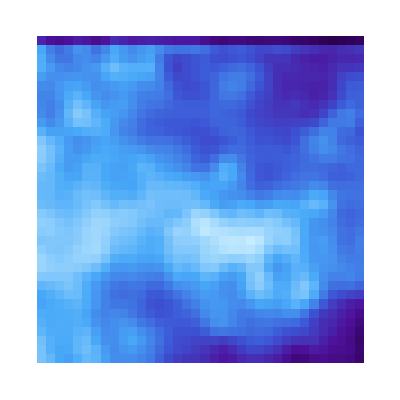

```mathematica
ArrayPlot[Partition[elevationdata,36],ColorFunction->Function[{x},ColorData["DeepSeaColors"][x]]]
```

Looking at the ArrayPlot of the water depths and the reversed ArrayPlot elevation data, we can see they look pretty similar. This means that the lower the elevation, there is generally more water. This result is similar to the Bathtub model, except there are a few differences that distinguish the two. On larger datasets, this information can be helpful for disaster mitigation.